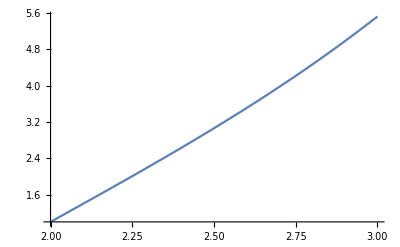

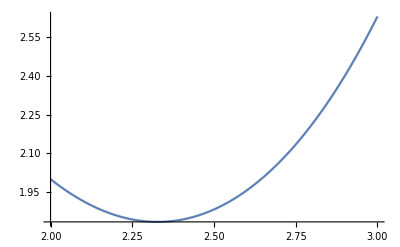

-1-(3 ⅇ^(2-t))/2+(3 ⅇ^(-2+t))/2+t

1+(3 ⅇ^(2-t))/2+(3 ⅇ^(-2+t))/2-t

```mathematica
sol=DSolve[{a'[t]==t + b[t],b'[t]==a[t]-t,a[2]==1,b[2]==2},{a,b}, {t, 2, 3}];
x[t_]:=a[t]/.sol[[1]]
y[t_]:=b[t]/.sol[[1]]
Plot[x[t],{t, 2, 3}]
Plot[y[t],{t, 2, 3}]
x[t]
y[t]
```